# Лабораторная работа №12

# Определение петли гистерезиса ферромагнетика магнитооптическим методом

## Нехаев Александр 654 гр.

Цель работы: ознакомиться с принципами применения магнитооптических методов для исследования прозрачных магнетиков; определить магнитные параметры исследуемого образца; изучить основы и принципы применения вычислительной техники для организации автоматизированного сбора и анализа экспериментальных данных физического эксперимента.

## Теоретическое описание

Ферромагнетик в отсутствие внешнего поля может обладать значительной намагниченностью, вызванной упорядочиванием магнитных моментов из-за внутренних взаимодействий, главным образом обменного. Возникающая магнитная структура представляет собой домены – области однородной намагниченности, разделённые доменными стенками. Её форма определяется уже более слабыми взаимодействиями, которые зависят от магнитостатической энергии структуры, кристаллографической анизотропии, энергии доменных границ, энергии взаимодействия с внешним магнитным полем.

Зависимость намагниченности ферромагнетика, для которого в начальном состоянии I и H равны нулю, показана на рисунке:

-Graphics-

Кривая намагниченности ферромагнетика

В слабых полях рост намагниченности вызван ростом момента одних областей за счёт уменьшения других в результате сдвига границ. В сильных полях происходит поворот момента отдельных областей по полю, достигается насыщение. Если после получения основной кривой намагничивания постепенно убрать внешнее поле, то намагниченность вещества уже не ляжет на ту же кривую из-за произошедших необратимых изменений. Для обращения намагниченности образца в нуль необходимо приложить поле, называемое коэрцитивной силой. Это явление называется магнитным гистерезисом. На рисунке 2 представлена типичная петля гистерезиса.

-Graphics-

Петля гистерезиса

Физически гистерезис вызван наличием неоднородностей в образце, таких как дислокации, пустоты и другие, из за которых движение доменных стенок может встречать потенциальные барьеры или ямы.

## Экспериментальная установка

Измерение петли гистерезиса проводится магнитооптическим методом с использованием эффекта Фарадея, который заключается во вращении плоскости поляризации линейно поляризованного света при прохождении намагниченного вещества.

-Graphics-

Блок-схема установки: 1 - лазер, 2 - образец, 3 - катушка, 4 – анализатор, 5 – фотоприёмник, 6 – усилитель, 
7 – амперметр, 8 – резистор, 9 – виртуальный осциллограф, 10 – генератор переменного напряжения.

Лазер излучает линейно поляризованный свет, который проходит через образец с намагниченностью I, плоскость поляризации поворачивается на некоторый угол ψ, пропорциональный проекции намагниченности на вектор распространения света. Затем луч идет через анализатор, который представляет собой поляроид. Интенсивность выходного сигнала изменяется в соответствии с законом Малюса: I_out=I_in cos^2(θ), где θ – угол между плоскостью поляризации входного излучения и разрешенным направлением поляроида. Далее луч света обрабатывается фотоприёмником, выходной сигнал подается на канал 1.

Если γ – начальный угол между плоскостью поляризации света, выходящего непосредственно из лазера, и разрешенным направлением поляроида, то угол θ по прохождении исследуемого образца будет равен сумме начального угла γ и приращения ψ, вносимого намагниченным веществом. Осуществляя регулировку тока через катушку, мы можем менять внешнее магнитное поле, а, следовательно, и намагниченность в соответствии с зависимостью вида гистерезисной кривой:

U=U_0 cos^2(γ+ψ)

Учитывая малость угла вращения ψ:

U=U_0/2(cos(2γ)-2ψ*sin(2γ)+1)

То есть, выходное напряжение фотоприемника пропорционально углу вращения, а значит и намагниченности вещества. Напряжение же на резисторе пропорционально величине внешнего магнитного поля Н.

## Ход работы

Найдём эффективную величину тока, текущую в катушке при напряжении питания 25 В: I=2 А. Тогда I_max:

```mathematica
Print[TraditionalForm[N[2*√2]], " А"]
```

2.82843 А

Проведем измерение зависимости намагниченности образца от внешнего поля. Коэффициент калибровки катушки: 150 Э/А.

Из графика получим, что:

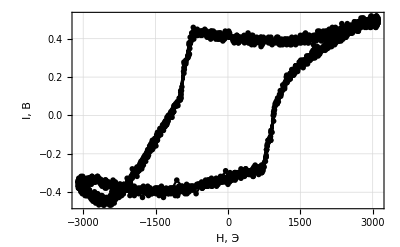

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Nekhaev_01.04.2019.xlsx"][[1]][[2;;All,2;;3]];
i=2*√2;
uMax=Max[data[[All,1]]];
r=uMax/i;
dataE=Transpose[{data[[All,2]]/r*150,data[[All,1]]}];
ListLinePlot[dataE,PlotTheme->"Detailed",FrameLabel->{"H, Э","I, В"}]
```

Кривая гистерезиса

коэрцитивная сила H_c:

```mathematica
distancesToX=Abs[EuclideanDistance[#,{#[[1]],0}]&/@dataE];
nearest=Position[distancesToX,Min[distancesToX]][[1,1]];
coercitio=Abs[Round[dataE[[nearest]][[1]]]];
Print["≈",coercitio," Э"]
```

≈1207 Э

Поле насыщения H_s:

```mathematica
distances=EuclideanDistance[#,{0,0}]&/@dataE;
farest=Ordering[distances,-1][[1]];
field=Round[dataE[[farest]][[1]]];
Print["≈",field," Э"]
```

≈3110 Э

## Вывод

В ходе работы нам удалось построить кривую гистерезиса для ферромагнитного образца и найти некоторые его параметры: коэрцитивную силу H_c≈1207 Э, и поле насыщения H_s≈3110 Э.